```mathematica
(*all errors are N(0,1); data is real, but may be scaled to an order of magnitude that puts the error between 1% or 10%*)
```

```mathematica
Table[x,{x,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
(*just x*)
```

```mathematica
Table[x+RandomVariate[NormalDistribution[0,1]],{x,1,25}]
```

{1.78911,0.62553,2.01295,5.00472,5.33279,6.99715,8.56787,7.61004,8.81425,9.42831,9.79978,10.1006,11.3555,12.6809,14.3768,14.8353,16.7808,16.0585,19.5048,20.0614,21.8866,21.4971,23.3099,26.9678,25.1561}

```mathematica
(*trajectory of bullet shot straight up at 250m/s (in hundreds of meters) no air resistance*)
```

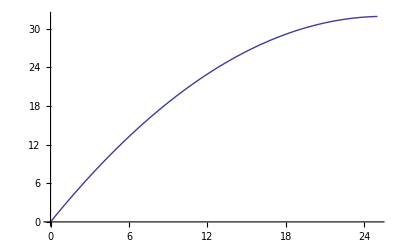

```mathematica
Plot[(-4.9*x^2+250*x)/100,{x,0,25}]
```

```mathematica
Table[(-4.9*x^2+250*x)/100+RandomVariate[NormalDistribution[0,1]],{x,1,25}]
```

{2.63506,5.05142,7.58814,8.36867,9.89025,12.6742,14.9608,17.1504,18.25,19.6037,21.9566,22.7667,24.1432,24.437,25.9185,26.0995,27.685,28.1738,28.8522,30.8774,29.6592,30.8546,30.6832,32.2816,31.9304}

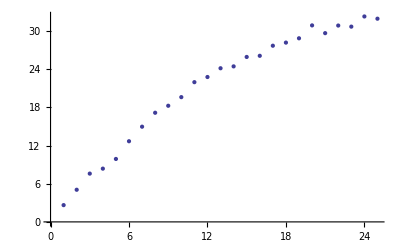

```mathematica
ListPlot[{2.635059591941196,5.051415955571876,7.58813637607227,8.368666818852493,9.89024909209137,12.674190611845187,14.96078788415249,17.150440616465918,18.249985871248654,19.60374416524068,21.95655990428961,22.766748016459772,24.143166969558685,24.436979150014515,25.91852289075169,26.099532019069898,27.685028434374892,28.17381873101912,28.852193511841755,30.87737709297303,29.659192161928623,30.85457388734584,30.683231100612936,32.28160751573607,31.93035301521347}]
```

```mathematica
Table[(-4.9*x^2+250*x)/100+RandomVariate[NormalDistribution[0,1]],{x,1,50}]
```

{2.80835,5.36042,8.41624,9.91429,12.0927,13.6851,14.5968,12.8428,19.5997,19.5701,20.5787,22.1903,23.551,23.9111,25.8426,25.5251,26.8011,28.7063,28.198,30.9035,31.105,29.8912,31.8577,30.5153,31.6658,31.818,33.4064,31.0855,30.9367,32.774,30.1629,29.2557,29.2816,27.7842,28.006,26.9055,23.3742,24.9058,24.2249,24.1884,20.3852,17.268,16.8667,13.0869,11.5819,10.5632,10.7766,5.94364,4.09698,2.99891}

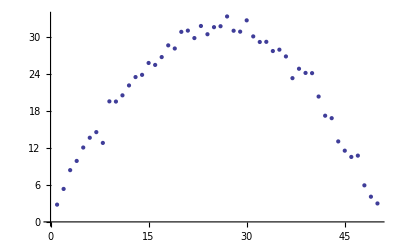

```mathematica
ListPlot[{2.8083529098112407,5.360417032205909,8.416235422149732,9.914289992575446,12.0927447376725,13.68509474552405,14.596815530583378,12.84276239409478,19.59974047163093,19.57013317153845,20.5786748199416,22.19034582454556,23.551046810913068,23.911123457401,25.842580060547764,25.525051082046097,26.80113748804807,28.70633983195526,28.19803621645759,30.903518295396555,31.105010293256356,29.89124668020534,31.85765884238815,30.515290659942437,31.665773426598225,31.818036544606606,33.40638909623992,31.085509014385206,30.936661838434862,32.774010610772955,30.162882661646055,29.255686695148057,29.28164380648313,27.784180676731808,28.00598706521938,26.905451554081793,23.374199983312497,24.905802684343502,24.224943446047625,24.188417418868447,20.38516328403662,17.267956746067426,16.866680626785932,13.086931052456125,11.581939683452802,10.563175504566303,10.776635587352793,5.943642666806181,4.096981419600855,2.9989145070886236}]
```

```mathematica
(*damped harmonic oscillator; beta = friction/2m; *)
```

```mathematica
x0=10;v0=20;beta=1/10;omega=1;
```

```mathematica
E^(-beta*t)*(x0*Cos[omega*t]+(beta*x0+v0)/omega *Sin[omega*t])
```

ⅇ^(-t/10) (10 Cos[t]+21 Sin[t])

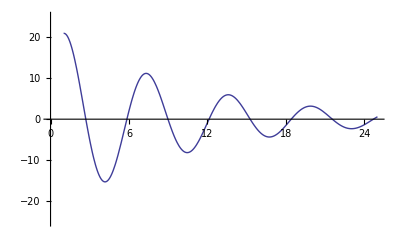

```mathematica
Plot[E^(-beta*t)*(x0*Cos[omega*t]+(beta*x0+v0)/omega *Sin[omega*t]),{t,1,25},PlotRange->{{0,25},{-25,25}}]
```

```mathematica
Table[E^(-beta*t)*(x0*Cos[omega*t]+(beta*x0+v0)/omega *Sin[omega*t])+RandomVariate[NormalDistribution[0,1]],{t,1,25}]
```

{20.4388,11.1238,-4.39306,-15.2666,-8.83603,2.95402,10.6062,7.45964,0.1444,-8.34118,-7.56731,-3.08952,3.9061,4.388,1.12161,-3.26213,-5.39157,0.578177,3.57381,3.07006,2.1935,-1.25449,-2.06437,-0.404703,1.84}

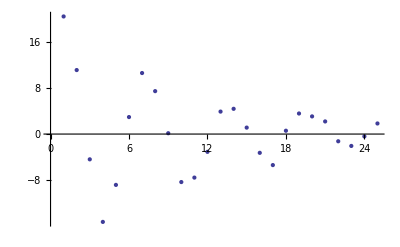

```mathematica
ListPlot[{20.438809919319155,11.123777637611314,-4.393062802352463,-15.266561275689375,-8.836028917453934,2.954018016351281,10.606229007729045,7.45963868163728,0.14440028329137078,-8.341182108773172,-7.567308214598575,-3.089520664366032,3.9061012763570626,4.387999683914941,1.121608786468672,-3.2621346344263022,-5.391572524189788,0.5781773032042266,3.5738104573505387,3.070063907864874,2.193498314968796,-1.2544883405357776,-2.064373632378543,-0.40470258482677657,1.8400006745769635}]
```

```mathematica
(*pure fibonaccci numbers; no error*)
```

```mathematica
Table[Fibonacci[x],{x,1,25}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025}

```mathematica
(*Half-life of iodinated contrast (hours)*)
```

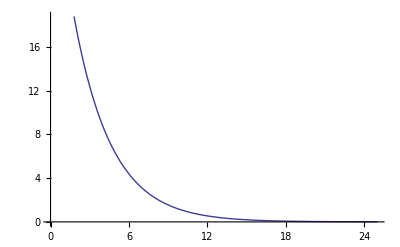

```mathematica
Plot[35*E^(Log[2]/2*-t),{t,0,25}]
```

```mathematica
Table[35*E^(Log[2]/2*-t)+RandomVariate[NormalDistribution[0,1]],{t,1,25}]
```

{25.053,18.3075,12.317,9.04931,8.58556,5.97653,3.17124,3.22191,1.99887,0.809647,1.95868,1.91115,-0.39391,-0.272709,0.742387,0.837293,-0.828464,-1.4348,0.324813,0.377846,-1.97081,0.383253,0.949264,-1.27316,-1.42841}

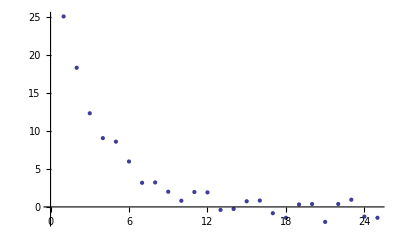

```mathematica
ListPlot[{25.053012666635404,18.307535790587867,12.317004125850717,9.04930812832133,8.585560297187655,5.976530460309115,3.17124489157928,3.221914551674616,1.9988657550949762,0.8096466625181784,1.9586820988260611,1.911147903223737,-0.3939099607778674,-0.27270928095797253,0.7423872671447493,0.8372933878579407,-0.8284642526311581,-1.4348005012621456,0.3248126664570496,0.37784619773474204,-1.970806513762634,0.3832534040192881,0.9492642672021567,-1.2731648732583514,-1.428412129698004}]
```

```mathematica
(*Chymotrypsin reaction rate under the michaelis-menten enzyme model,x-concentration and f(x) is reaction rate*)
```

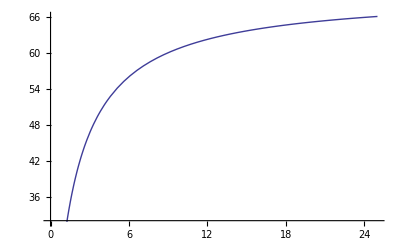

```mathematica
Plot[500*.14x/(1.5 +x),{x,0,25}]
```

```mathematica
Table[500*.14x/(1.5 +x)+RandomVariate[NormalDistribution[0,1]],{x,1,25}]
```

{26.4847,40.5327,46.0789,49.2011,52.8957,55.7521,58.6808,60.4513,60.7341,62.8158,61.3433,63.3663,61.8981,64.8282,64.0561,66.5473,62.2379,66.023,65.5182,66.5476,63.9284,64.9167,65.3217,66.3098,66.0502}

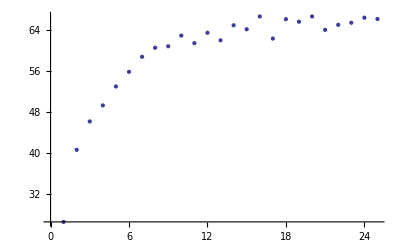

```mathematica
ListPlot[{26.48471175958366,40.53273672538648,46.07890739099391,49.20106644561016,52.895713929068236,55.75208233849938,58.680818021522775,60.45125923714944,60.73408409133091,62.81580221367641,61.34332449720761,63.366322003684594,61.898083662923504,64.82821084450389,64.05606107709495,66.54726677177399,62.23789598815002,66.02304191245362,65.51815151465223,66.54763973050902,63.928409430859716,64.91665966414745,65.32173014025689,66.30976407924153,66.050247294222}]
```

```mathematica
k=100;p=2;r=1/2;
```

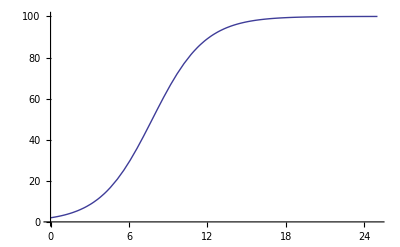

```mathematica
Plot[k*p*E^(r*t)/(k+p*(E^(r*t)-1)),{t,0,25}]
```

```mathematica
Table[k*p*E^(r*t)/(k+p*(E^(r*t)-1))+RandomVariate[NormalDistribution[0,1]],{t,1,25}]
```

{2.17125,5.76369,6.57743,13.7159,19.9859,29.3505,38.9081,52.8789,65.0323,74.9715,84.7898,89.6009,93.4051,95.6506,97.506,98.5871,98.0788,97.754,100.191,98.8393,103.014,100.366,101.992,101.659,98.8561}

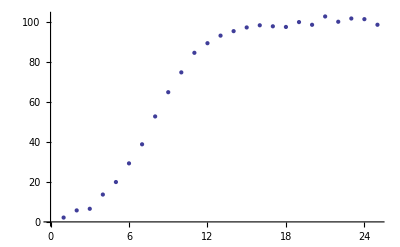

```mathematica
ListPlot[{2.171247825894163,5.763689126117891,6.5774344385673995,13.715897853103497,19.98586780395752,29.350513846875213,38.90813411111161,52.87892919728454,65.03234025890367,74.97153523349792,84.78979797102232,89.6009438394518,93.40510862204678,95.65058315728602,97.50601191805117,98.58706525291807,98.07875358474854,97.75404851873738,100.19130954761465,98.83929461132081,103.01443117705959,100.36562563067278,101.99213155248908,101.65908625631019,98.8561038283989}]
```

```mathematica
(*hubbert peak oil curve in 100-million barrels,
6% growth, 200 gigabarrels total and peak in 1970*)
```

```mathematica
q=2000;a=70;b=.06;
```

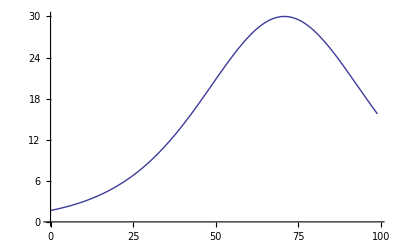

```mathematica
Plot[(a b ⅇ^(-b t) q)/((1+a ⅇ^(-b t))^2),{t,0,99}]
```

```mathematica
Table[(a b ⅇ^(-b t) q)/((1+a ⅇ^(-b t))^2)+RandomVariate[NormalDistribution[0,1]],{t,0,99}]
```

{2.47792,1.66126,1.29464,1.45541,1.91928,1.7015,1.76235,4.30153,1.97041,2.10179,1.81996,3.04693,2.62143,3.30383,3.79316,1.92067,2.82471,5.59357,4.40778,3.93959,5.39259,6.37814,5.35129,5.40325,7.37639,7.4691,5.38406,7.84323,6.74289,7.62103,8.37723,9.33054,10.2963,11.6003,11.2796,10.397,10.4913,11.8025,11.9236,12.5397,14.4816,13.6076,15.3405,14.3081,15.7918,17.7835,17.2168,18.9163,19.1872,20.0249,19.9648,21.1897,22.8019,22.9909,22.5857,24.5689,24.2836,25.4936,26.5273,26.3809,27.4156,26.1805,27.602,27.5581,30.7774,31.1848,28.5914,28.4669,30.3312,28.8426,28.6371,29.5687,29.8155,28.7657,29.9785,30.1336,29.7337,28.2382,29.3158,30.1079,28.3529,27.7694,27.8894,26.0385,26.7129,23.8395,25.9024,23.076,23.1135,22.1821,19.8199,20.8983,20.1177,20.8961,19.9535,18.3276,18.9358,17.7117,14.3427,15.0427}

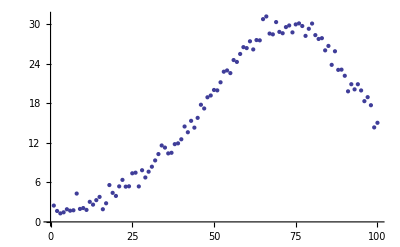

```mathematica
ListPlot[{2.4779216760483878,1.6612622619496022,1.294641980542206,1.4554137363619748,1.9192780760299903,1.7015004335362276,1.7623483409911718,4.301533309829179,1.970405297226586,2.1017885773818787,1.8199609261062348,3.04692859082872,2.6214304005016213,3.303826675023561,3.793161790069753,1.9206744795625341,2.8247125454203013,5.593566805118046,4.407777701163172,3.9395850503717034,5.392591216158935,6.378140959846144,5.3512886483806605,5.403249031155189,7.376394653724299,7.469103582187184,5.384056644689113,7.8432327516778475,6.742892601066142,7.621033545190755,8.377227368154102,9.33054244009095,10.296292256169483,11.600300809617632,11.27961818039837,10.396954330445343,10.491311850605417,11.80250766931221,11.923594035538816,12.539689394877234,14.481594721146761,13.607585604108237,15.340547977310344,14.308100772552947,15.791828491323852,17.783502063206353,17.216773184098805,18.91634375307278,19.187237587217528,20.02492426846102,19.9647653440674,21.189698351819573,22.801864060874628,22.990867300203874,22.585702927162334,24.56886845936111,24.283590957090084,25.493618617073885,26.527339626725,26.380923205835558,27.415619847301347,26.180527002884592,27.60203340351428,27.558080866434914,30.777364164020067,31.184797245356922,28.59136142502595,28.466903034557003,30.331226043884552,28.842583752886107,28.637068393025658,29.56866266987844,29.815541080434684,28.76573848259256,29.978481904749522,30.133564287327665,29.733723033510007,28.238240418795254,29.315753651027187,30.107875220579484,28.352930931194514,27.769355726349524,27.88938009491887,26.038461984602563,26.712869720426244,23.839514789231053,25.902376116007257,23.07602293843935,23.113482362529812,22.182129217648903,19.81991936381271,20.898328785561706,20.117740450477136,20.896053370751922,19.953541007955995,18.327577899219207,18.935816404776062,17.711692540962545,14.342685833000578,15.04273408860696}]
```

```mathematica
(*IQ scores of 1200 people*)
```

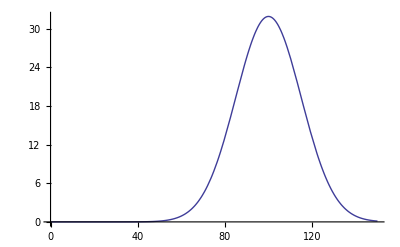

```mathematica
Plot[1200*E^(-(x-100)^2/(2*15^2))/Sqrt[2*Pi*15^2],{x,0,150}]
```

```mathematica
Table[1200*E^(-(x-100)^2/(2*15^2))/Sqrt[2*Pi*15^2]+RandomVariate[NormalDistribution[0,1]],{x,50,149}]
```

{1.37566,-0.899212,0.588958,0.613957,0.67308,-0.240921,0.731746,-0.843862,0.751699,2.28214,1.1486,1.79116,1.52875,0.731629,0.92356,0.885134,3.16097,2.0485,3.64488,5.75456,2.74511,5.31514,6.20542,5.97012,5.67394,7.79638,8.75234,10.0676,11.318,11.2768,13.3625,15.3951,15.9025,16.107,17.5867,18.7222,20.315,22.2963,22.4823,23.189,26.4283,27.3979,27.9506,29.7377,29.606,31.2871,30.71,30.4486,31.0699,31.9716,32.1896,29.7381,34.3681,30.9706,32.4324,30.443,30.3364,27.4615,29.8134,26.7659,24.6115,23.9923,22.0388,22.2489,20.6744,19.4673,17.7974,14.4444,15.4269,13.9571,11.2766,12.2884,12.5268,10.2402,8.29488,8.5,8.17637,5.07055,5.53863,5.42583,4.69913,1.45667,3.19444,4.62804,2.04399,2.32917,0.92009,1.79705,0.223042,2.75132,0.464375,-0.00995843,0.0591558,1.28974,-0.879947,-0.156615,0.435686,0.447098,-1.62389,0.962722}

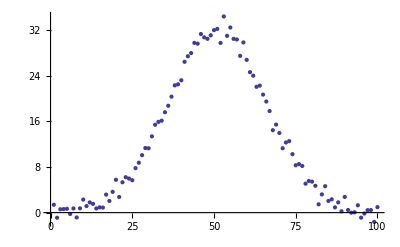

```mathematica
ListPlot[{1.3756624751801771,-0.8992115047508501,0.588957574818409,0.6139566173642812,0.6730802336965944,-0.24092115165014322,0.7317464663400912,-0.8438619811476984,0.7516990107559423,2.282137231975948,1.1486033813618375,1.7911584350116916,1.528749563031728,0.7316293875347247,0.9235603023415013,0.8851343332063879,3.160967381265383,2.048499028634417,3.6448756042381856,5.7545647235416935,2.745108568850795,5.31513575496763,6.205416186157054,5.970124559562409,5.673943921141336,7.796376880919425,8.752344330538552,10.067626185514696,11.317986421423628,11.276848100400953,13.362539178232021,15.395101668940693,15.902527299719567,16.106979596005925,17.58674290337903,18.72221428731676,20.315023892625657,22.296294121195753,22.482322773704222,23.189034918973856,26.428312461514956,27.397899884368133,27.95061554170385,29.737748739944127,29.605967227799585,31.287119219365728,30.71004518699536,30.448568807199702,31.069880395585653,31.97160613187758,32.18958833080663,29.73810397104459,34.36814860242857,30.97063414110299,32.43242161294528,30.44304547129705,30.336446065730428,27.461511516493868,29.813366796561667,26.7658654298015,24.611541958779718,23.992337735113384,22.038849860565,22.24893693851881,20.67442661617606,19.467318101796206,17.79744600908019,14.444440505001637,15.426909585894558,13.957099171651182,11.276594367274388,12.28844390413152,12.526792497274542,10.240192454646799,8.294875302855182,8.5000003406172,8.17637195056099,5.070548765366016,5.538631914841893,5.42583080443652,4.699126632828658,1.4566674085948756,3.194435757349053,4.628039412904675,2.0439859286727975,2.3291734786460876,0.9200899903580995,1.797046690270924,0.22304243185712846,2.7513152353498054,0.46437521514826857,-0.009958429078189002,0.05915580873016557,1.2897358727865558,-0.8799472797659301,-0.15661520043500526,0.435686071657575,0.447098258539369,-1.6238909830476704,0.9627224634303911}]
```